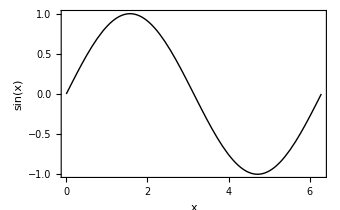

```mathematica
Plot[Sin[x],{x,0,2 Pi},PlotStyle->{Thick,Black},Frame->True,FrameLabel->{"x","sin(x)"},LabelStyle->{FontFamily->"Times",FontSize->16},TicksStyle->Directive[FontFamily->"Times",FontSize->14],ImageSize->{340,Automatic},PlotRange->All]
```

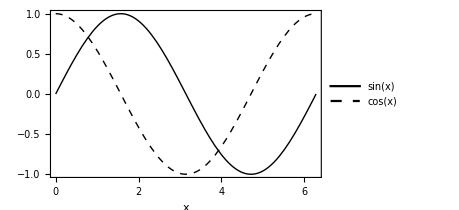

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2 Pi},PlotStyle->{{Thick,Black},{Thick,Dashed, Black}},Frame->True,FrameLabel->{"x",None},LabelStyle->{FontFamily->"Times",FontSize->16},TicksStyle->Directive[FontFamily->"Times",FontSize->14],PlotLegends->Placed[{"sin(x)","cos(x)"},{0.2,0.15}],ImageSize->{340,Automatic}]
```

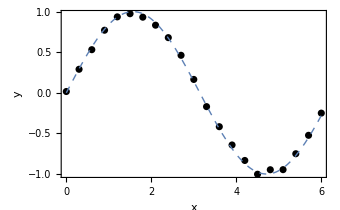

```mathematica
dataExample=Table[{x,Sin[x]+RandomReal[{-0.05,0.05}]},{x,0,6,0.3}];

Show[ListPlot[dataExample,PlotStyle->{Black,PointSize[0.015]},Frame->True],Plot[Sin[x],{x,0,6},PlotStyle->{Thick,Dashed}],FrameLabel->{"x","y"},LabelStyle->{FontFamily->"Times",FontSize->16},TicksStyle->Directive[FontFamily->"Times",FontSize->14],ImageSize->{340,Automatic}]
```

```mathematica
ClearAll[PRDStyle,PRDPlot];

(*Common APS/PRD style settings*)
PRDStyle={Frame->True,Axes->False,PlotRange->All,PlotStyle->Thick,FrameStyle->Directive[Black,Thickness[0.003]],FrameTicksStyle->Directive[FontFamily->"Times",FontSize->14],LabelStyle->{FontFamily->"Times",FontSize->16},ImageSize->{340,Automatic} (* ~single-column width,APS standard*)};

(*Wrapper for Plot with PRD style*)
PRDPlot[expr_,range__,opts:OptionsPattern[]]:=Plot[expr,range,Evaluate@FilterRules[{opts},Options[Plot]],Evaluate@PRDStyle];
```

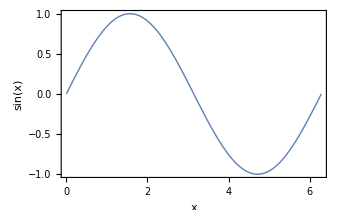

```mathematica
PRDPlot[Sin[x],{x,0,2 Pi},FrameLabel->{"x","sin(x)"}]
```

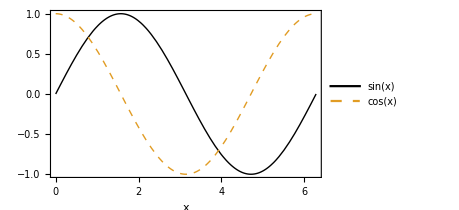

```mathematica
PRDPlot[{Sin[x],Cos[x]},{x,0,2 Pi},PlotStyle->{{Thick,Black},{Thick,Dashed}},FrameLabel->{"x",None},PlotLegends->Placed[{"sin(x)","cos(x)"},{0.8,0.85}]]
```

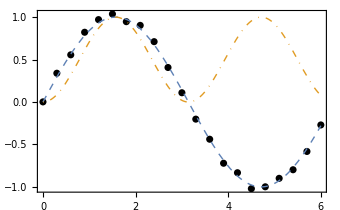

C:\Users\ilham\Dropbox\Riset-riset\00 Pak Bobby, Pak Agus, dan Kevin\runTOV\examplePlot1.eps

```mathematica
dataExample=Table[{x,Sin[x]+RandomReal[{-0.05,0.05}]},{x,0,6,0.3}];

Show[ListPlot[dataExample,PlotStyle->{Black,PointSize[0.015]},Evaluate@PRDStyle, PlotLegends->Placed[{"Data"},{0.2,0.25}]],PRDPlot[{Sin[x],Sin[x]^2},{x,0,6},PlotStyle->{{Thick,Dashed},{Thick,DotDashed}},PlotLegends->Placed[{"Sin(x)","Sin^2(x)"},{0.2,0.25}]]]
Export[FileNameJoin[{NotebookDirectory[],"examplePlot1.eps"}],%]
```

```mathematica
Join
```

```mathematica
(*Export["figure1.pdf",%]   (*best for LaTeX*)
Export["figure1.eps",%]   (*also accepted by APS*)
Export["figure1.tif",%,ImageResolution->600]   (*if raster is required*)*)
```